```mathematica
data = {{1,1},{2,2},{3,3},{4,5},{5,7},{6,11},{7,15},{8,22},{9,30},{10,42},{11,56},{12,77},{13,101},{14,135},{15,176},{16,231},{17,297},{18,385},{19,490},{20,627},{21,792},{22,1002},{23,1255},{24,1575},{25,1958},{26,2436},{27,3010},{28,3718},{29,4565},{30,5604},{31,6842},{32,8349},{33,10143},{34,12310},{35,14883},{36,17977},{37,21637},{38,26015},{39,31185},{40,37338},{41,44583},{42,53174},{43,63261},{44,75175},{45,89134},{46,105558},{47,124754},{48,147273},{49,173525},{50,204226},{51,239943},{52,281589},{53,329931},{54,386155},{55,451276},{56,526823},{57,614154},{58,715220},{59,831820},{60,966467},{61,1121505},{62,1300156},{63,1505499},{64,1741630},{65,2012558},{66,2323520},{67,2679689},{68,3087735},{69,3554345},{70,4087968},{71,4697205},{72,5392783},{73,6185689},{74,7089500},{75,8118264},{76,9289091},{77,10619863},{78,12132164},{79,13848650},{80,15796476},{81,18004327},{82,20506255},{83,23338469},{84,26543660},{85,30167357},{86,34262962},{87,38887673},{88,44108109},{89,49995925},{90,56634173},{91,64112359},{92,72533807},{93,82010177},{94,92669720},{95,104651419},{96,118114304},{97,133230930},{98,150198136},{99,169229875},{100,190569292}};
model=a Exp[b x]+c;
fit=FindFit[data,model, {a, {b,1}, {c,First@Mean[data]}}, x]
modelf=Function[{t},Evaluate[model/.fit]]
Plot[modelf[t],{t,0,100}]
```

{a→8.44965×10^-36,b→1.,c→1.28367×10^7}

Function[{t},1.28367×10^7+8.44965×10^-36 ⅇ^(1. x)]

-Graphics-

```mathematica
$GeoLocation=GeoPosition[{22.8885312,-109.9128402}] 
GeoListPlot[GeoNearest["Volcano",Here,10]]
```

GeoPosition[{22.8885,-109.913}]

-Graphics-

```mathematica
Sunset[Here]
Sunrise[Here]
MoonPhase[Now]
```

Sun 12 Jun 2016 20:07GMT-6.

Mon 13 Jun 2016 06:35GMT-6.

0.5688

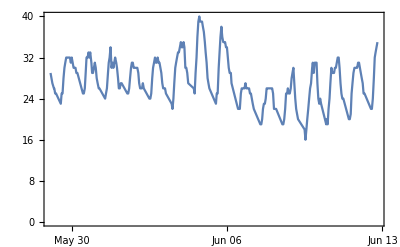

```mathematica
DateListPlot[AirTemperatureData[Here,{DatePlus[Today, -Quantity[2, "Weeks"]],Now}]]
```

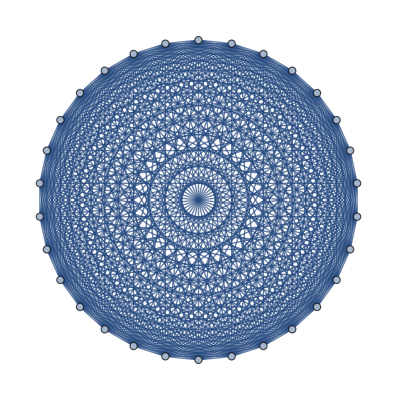

```mathematica
CompleteGraph[30]
```

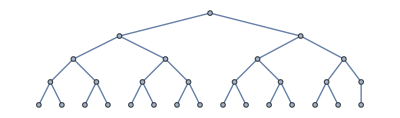

```mathematica
KaryTree[30]
```

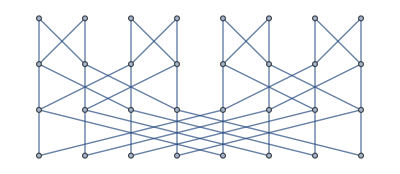

```mathematica
ButterflyGraph[3]
```

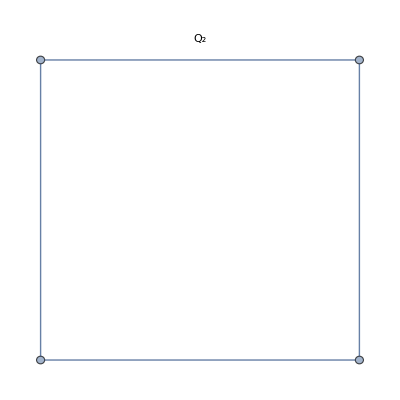
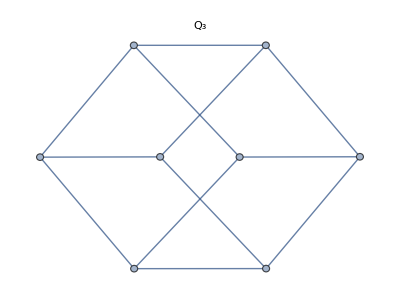
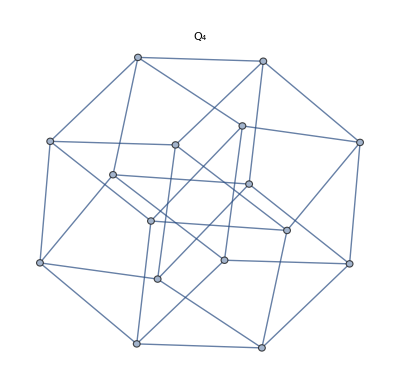

```mathematica
Table[HypercubeGraph[i,PlotLabel->Subscript[Q,i]],{i,2,4}]
```

```mathematica
AdjacencyMatrix[RandomGraph[{5,5}]]
```

SparseArray[<10>, {5, 5}]

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
NestList[Rotate[Framed[#],RandomReal[{0,2π}]]&,Rasterize[Style["A"],50],3]
```

{Rasterize[A,50],Rasterize[A,50],Rasterize[A,50],Rasterize[A,50]}

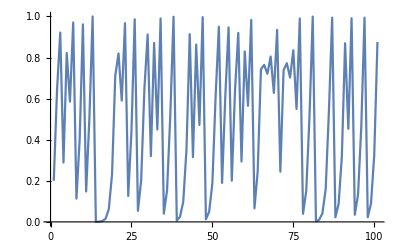

```mathematica
ListLinePlot[NestList[4#(1-#)&,0.2,100]]
```

```mathematica
Nest[1+1/#&,1,30]//N
```

1.61803

```mathematica
NestList[3*#&,1,10] (* powers of three *)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

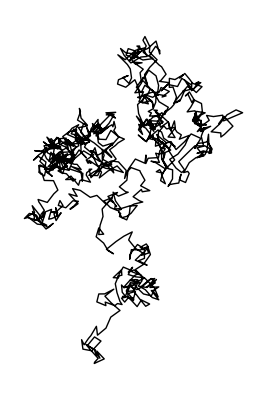

```mathematica
Graphics[Line[NestList[#+RandomReal[{-1,1},2]&,{0,0},1000]]] (*pg160 27.8*)
```

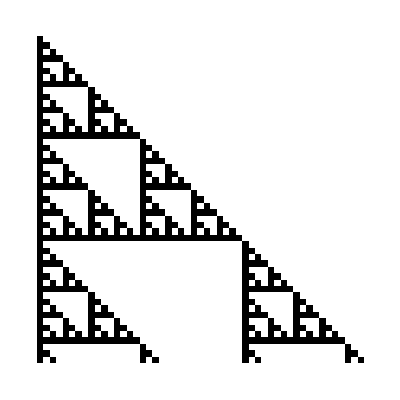

```mathematica
(* Pascal's triangle mod 2 *)
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

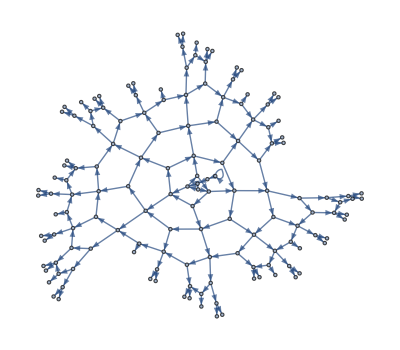

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

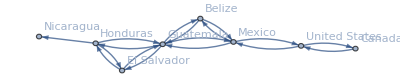

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->All]
```

```mathematica
Select[WordList[],StringTake[#,1]==StringTake[StringReverse[#],1]=="p"&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,payslip,peep,penmanship,pep,pickup,pileup,pimp,pip,plop,plump,polyp,pomp,poop,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Select[Array[Prime,100],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[RomanNumeral[Range[100]],!MemberQ[Characters[#],"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[RomanNumeral[Range[1000]],#==StringReverse[#]&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
Select[Table[IntegerName[n],{n,100}],First[Characters[#]]==Last[Characters[#]]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[TextWords[WikipediaData["words"]],StringLength[#]>15&]
```

{orthographically,multiple-morpheme,Proto-Indo-European}

```mathematica
NestList[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

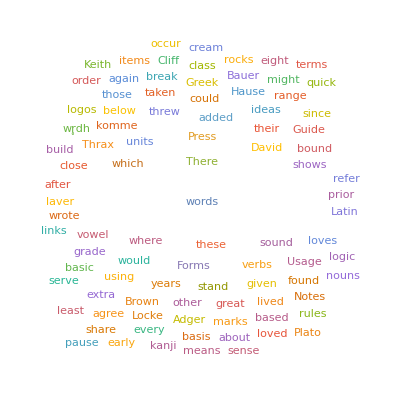

```mathematica
WordCloud[Select[TextWords[WikipediaData["words"]],StringLength[#]==5&]]
```

```mathematica
Select[WordList[],StringLength[#]≥3&&StringTake[#,3]==StringTake[StringReverse[#],3]&&#≠StringReverse[#]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[WordList[],StringLength[#]==10&&Total[LetterNumber[#]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clementine,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,impugnable,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}

```mathematica
Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Array[Prime[#+1]-Prime[#]&,20]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2}

```mathematica
Array[#1+#2&,{10,10}]//Grid
Array[Plus,{10,10}]//Grid
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
FoldList[Times,Range[10]]
FoldList[Times,1,Range[10]]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
FoldList[Times,Array[Prime,10]]
FoldList[Times,1,Array[Prime,10]]
```

{2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

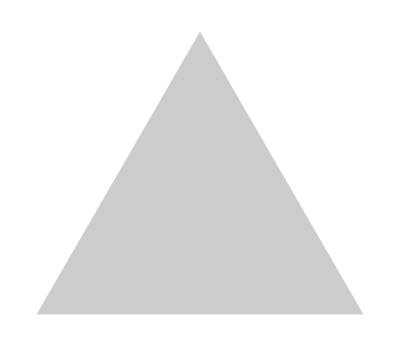
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FoldList[ImageAdd,Table[Graphics[Style[RegularPolygon[n],Opacity[0.2]]],{n,3,8}]]
```


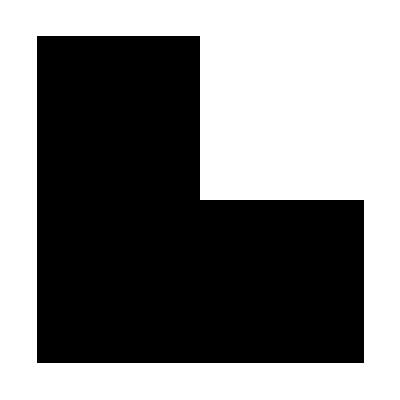
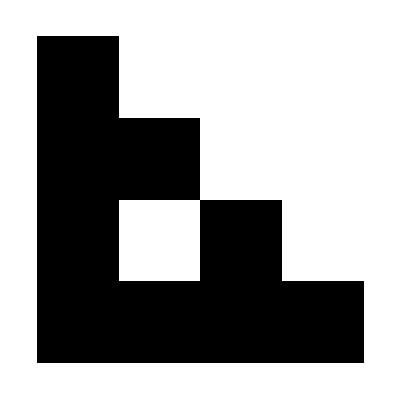

-Graphics-

```mathematica
(* Sierpinski pattern *)
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},8]]
```

```mathematica
Thread[Alphabet["English"]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
Partition[Alphabet["English"],4]//Grid
```

a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p
q | r | s | t
u | v | w | x

```mathematica
Grid[Partition[Characters[StringTake[WikipediaData["words"],400]],20],Frame->All]
```

I | n |   | l | i | n | g | u | i | s | t | i | c | s | , |   | a |   | w | o
r | d |   | i | s |   | t | h | e |   | s | m | a | l | l | e | s | t |   | e
l | e | m | e | n | t |   | t | h | a | t |   | m | a | y |   | b | e |   | u
t | t | e | r | e | d |   | i | n |   | i | s | o | l | a | t | i | o | n |  
w | i | t | h |   | s | e | m | a | n | t | i | c |   | o | r |   | p | r | a
g | m | a | t | i | c |   | c | o | n | t | e | n | t |   | ( | w | i | t | h
  | l | i | t | e | r | a | l |   | o | r |   | p | r | a | c | t | i | c | a
l |   | m | e | a | n | i | n | g | ) | . |   | T | h | i | s |   | c | o | n
t | r | a | s | t | s |   | d | e | e | p | l | y |   | w | i | t | h |   | a
  | m | o | r | p | h | e | m | e | , |   | w | h | i | c | h |   | i | s |  
t | h | e |   | s | m | a | l | l | e | s | t |   | u | n | i | t |   | o | f
  | m | e | a | n | i | n | g |   | b | u | t |   | w | i | l | l |   | n | o
t |   | n | e | c | e | s | s | a | r | i | l | y |   | s | t | a | n | d |  
o | n |   | i | t | s |   | o | w | n | . |   | A |   | w | o | r | d |   | m
a | y |   | c | o | n | s | i | s | t |   | o | f |   | a |   | s | i | n | g
l | e |   | m | o | r | p | h | e | m | e |   | ( | f | o | r |   | e | x | a
m | p | l | e | : |   | o | h | ! | , |   | r | o | c | k | , |   | r | e | d
, |   | q | u | i | c | k | , |   | r | u | n | , |   | e | x | p | e | c | t
) | , |   | o | r |   | s | e | v | e | r | a | l |   | ( | r | o | c | k | s
, |   | r | e | d | n | e | s | s | , |   | q | u | i | c | k | l | y | , |

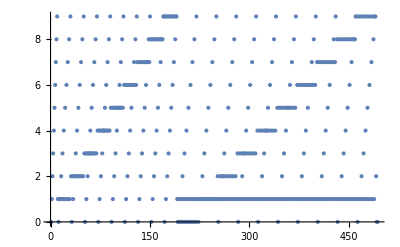

-Graphics-

```mathematica
(* Champernowne *)
ListPlot[Flatten[Table[IntegerDigits[n],{n,0,200}]]]
ListPlot[Flatten[IntegerDigits/@Range[0,200]]]
```

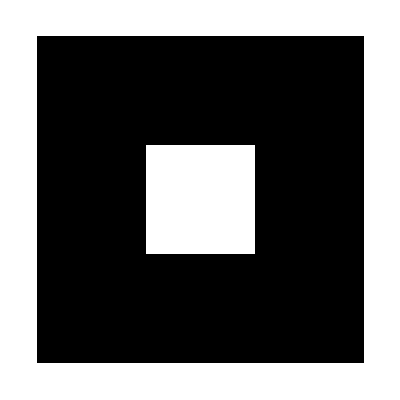
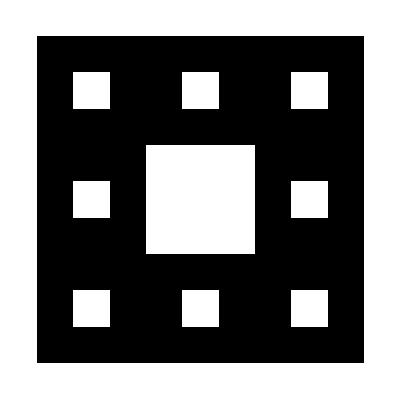
{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},2]
ArrayPlot[Nest[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]]
```

```mathematica
(* Pythagorean triples *)
Select[Flatten[Table[{x,y,√(x^2+y^2)},{x,20},{y,20}],1],IntegerQ[Last[#]]&]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

```mathematica
Table[Max[Length/@Split[IntegerDigits[2^n]]],{n,100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
GatherBy[Array[IntegerName,100],StringTake[#,1]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
Take[WordList[],50]
SortBy[Take[WordList[],50],StringTake[StringReverse[#],1]&]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,abbreviation,abdicate,abdication,abdomen,abdominal,abduct,abducting,abduction,abductor,abeam,abed,aberrant,aberration,abet,abettor,abeyance,abhor,abhorrence,abhorrent,abidance,abide,abiding,ability,abject,abjection,abjectly}

{a,abandoned,abashed,abbreviated,abed,abalone,abase,abate,abbe,abbreviate,abdicate,abeyance,abhorrence,abidance,abide,abducting,abiding,aah,abash,aardvark,aback,abdominal,abeam,abandon,abbreviation,abdication,abdomen,abduction,aberration,abjection,abattoir,abductor,abettor,abhor,abacus,abbess,abaft,abandonment,abasement,abashment,abatement,abbot,abduct,aberrant,abet,abhorrent,abject,abbey,ability,abjectly}

```mathematica
SortBy[Table[n^2,{n,20}],First@IntegerDigits[#]&]
```

{1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9}

```mathematica
SortBy[Array[IntegerName,20],StringLength[#]&]
SortBy[Range[20],IntegerName]
```

{one,six,ten,two,five,four,nine,eight,seven,three,eleven,twelve,twenty,fifteen,sixteen,eighteen,fourteen,nineteen,thirteen,seventeen}

{8,18,11,15,5,4,14,9,19,1,7,17,6,16,10,13,3,12,20,2}

```mathematica
GatherBy[RandomChoice[WordList[],20],StringLength]
```

{{manful,rabbet,bellow},{faker,soled,houri,shiny},{determiner},{cigarette,flashcard,cormorant,horsehair,resonator},{cylinder,polemics},{revolve,plywood,vitrine},{indissoluble},{unexploited}}

```mathematica
Intersection[EntityList[EntityClass["Country","NorthAtlanticTreatyOrganization"]],EntityList[EntityClass["Country","GroupOf8"]]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
Column/@Permutations[Range[4]]//Grid
```

Grid[{1
2
3
4,1
2
4
3,1
3
2
4,1
3
4
2,1
4
2
3,1
4
3
2,2
1
3
4,2
1
4
3,2
3
1
4,2
3
4
1,2
4
1
3,2
4
3
1,3
1
2
4,3
1
4
2,3
2
1
4,3
2
4
1,3
4
1
2,3
4
2
1,4
1
2
3,4
1
3
2,4
2
1
3,4
2
3
1,4
3
1
2,4
3
2
1}]

```mathematica
Union[StringJoin/@Permutations[Characters["hello"]]]
```

{ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,lehlo,lehol,lelho,leloh,leohl,leolh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lleho,lleoh,llheo,llhoe,lloeh,llohe,loehl,loelh,lohel,lohle,loleh,lolhe,oehll,oelhl,oellh,ohell,ohlel,ohlle,olehl,olelh,olhel,olhle,olleh,ollhe}

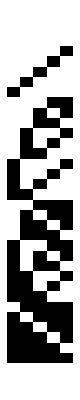
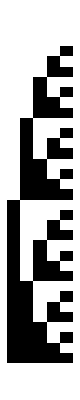
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[SortBy[Tuples[{0,1},5],Total[#]-5&]],ArrayPlot[SortBy[Tuples[{0,1},5],Total[#]&]],ArrayPlot[Tuples[{0,1},5]]}
```

```mathematica
Table[StringJoin[RandomChoice[Alphabet["English"],5]],10]
```

{ntjoc,mgwey,wmmmn,yrllv,rosnf,pfjxf,yvauv,iilqm,xxyeg,jvsoc}

```mathematica
Flatten[Table[{i,j,k},{i,2},{j,2},{k,2}],2]
Table[{i,j,k},{i,2},{j,2},{k,2}]
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

{{{{1,1,1},{1,1,2}},{{1,2,1},{1,2,2}}},{{{2,1,1},{2,1,2}},{{2,2,1},{2,2,2}}}}

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
Part[Alphabet[],Range[Length[Alphabet[]]/2.]*2]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

```mathematica
Take[Sort[Flatten[{#^2,#^3}&/@Range[20]]],10]
```

{1,1,4,8,9,16,25,27,36,49}

```mathematica
Position[TextWords[WikipediaData["computers"]],"software"]
```

{{4325},{4463},{4470},{4478},{4500},{5801},{5895},{5917},{7339},{7396},{7418}}

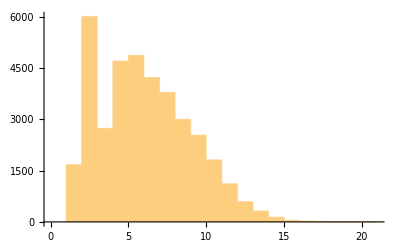

```mathematica
Histogram[Flatten[Position[Characters[#],"e"]&/@WordList[]]]
```

```mathematica
If[IntegerQ[Sqrt[#]],Red,#^3]&/@Range[100]
```

{RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]}

```mathematica
If[First[IntegerDigits[#]]<5,Nothing,#]&/@Array[Prime,100]
```

{5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541}

```mathematica
Grid[NestList[ReplacePart[#,RandomInteger[{1,Length[#]}]->Nothing]&,Range[10],9]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 8 | 9 | 10 | 
1 | 2 | 4 | 5 | 6 | 8 | 9 | 10 |  | 
2 | 4 | 5 | 6 | 8 | 9 | 10 |  |  | 
2 | 4 | 5 | 8 | 9 | 10 |  |  |  | 
4 | 5 | 8 | 9 | 10 |  |  |  |  | 
4 | 5 | 9 | 10 |  |  |  |  |  | 
5 | 9 | 10 |  |  |  |  |  |  | 
5 | 9 |  |  |  |  |  |  |  | 
9 |  |  |  |  |  |  |  |  |

```mathematica
Reverse[SortBy[WordList[],StringLength]][[1;;10]]
TakeLargestBy[WordList[],StringLength,10]
```

{electroencephalographic,electroencephalograph,uncharacteristically,magnetohydrodynamics,internationalization,electroencephalogram,counterrevolutionary,compartmentalization,buckminsterfullerene,straightforwardness}

{electroencephalographic,electroencephalograph,counterrevolutionary,buckminsterfullerene,compartmentalization,electroencephalogram,internationalization,uncharacteristically,magnetohydrodynamics,incomprehensibility}

```mathematica
Reverse[SortBy[Array[IntegerName,100],StringLength]][[1;;5]]
TakeLargestBy[Array[IntegerName,100],StringLength,5]
```

{seventy-three,seventy-seven,seventy-eight,twenty-three,twenty-seven}

{seventy-seven,seventy-three,seventy-eight,twenty-three,twenty-eight}

```mathematica
Array[IntegerName,100]
TakeLargestBy[Array[IntegerName,100],Count[Characters[#],"e"]&,5]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}

{seventy-three,seventeen,seventy-seven,nineteen,eleven}

```mathematica
FromDigits/@Select[IntegerDigits[Range[100,999]],First[#]==Last[#]&]
FromDigits/@Cases[IntegerDigits[Range[100,999]],{x_,__,x_}]
```

{101,111,121,131,141,151,161,171,181,191,202,212,222,232,242,252,262,272,282,292,303,313,323,333,343,353,363,373,383,393,404,414,424,434,444,454,464,474,484,494,505,515,525,535,545,555,565,575,585,595,606,616,626,636,646,656,666,676,686,696,707,717,727,737,747,757,767,777,787,797,808,818,828,838,848,858,868,878,888,898,909,919,929,939,949,959,969,979,989,999}

{101,111,121,131,141,151,161,171,181,191,202,212,222,232,242,252,262,272,282,292,303,313,323,333,343,353,363,373,383,393,404,414,424,434,444,454,464,474,484,494,505,515,525,535,545,555,565,575,585,595,606,616,626,636,646,656,666,676,686,696,707,717,727,737,747,757,767,777,787,797,808,818,828,838,848,858,868,878,888,898,909,919,929,939,949,959,969,979,989,999}

```mathematica
Cases[_Integer]@Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]]
```

{2,8,5,18,32,50,20,10,2,72,98,45,128,17,162,200,80,40,8}

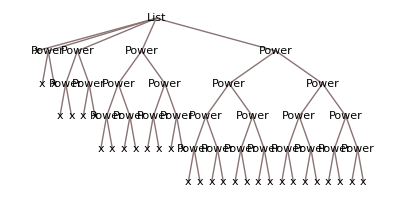

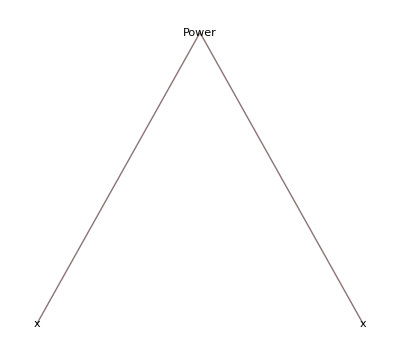
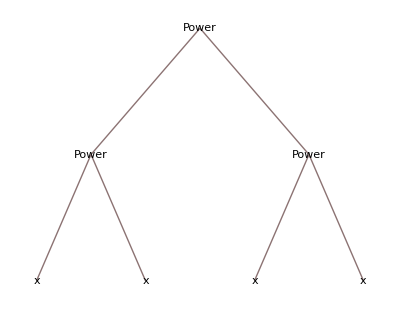
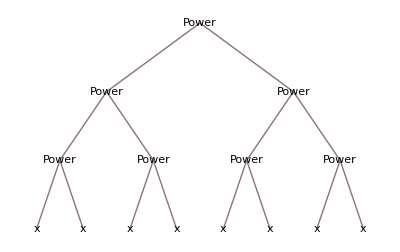
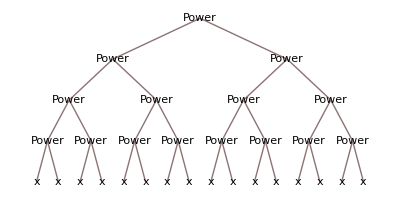
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeForm[FoldList[#^#&,x,Range[4]]]
TreeForm/@NestList[#^#&,x,4]
```

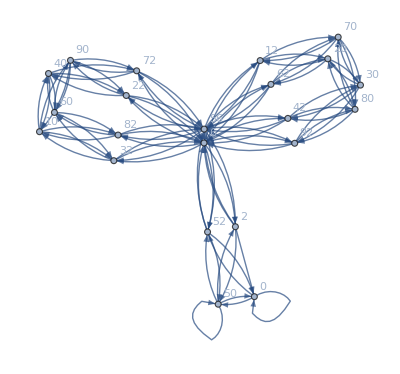

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1],VertexLabels->All]
```

```mathematica
Graph[Rule@@@Partition[TextWords[WikipediaData["computers"],200],2,1]]
```

-Graphics-

```mathematica
f@@@{{1,2},{7,2},{5,4}}
f[#]&/@{{1,2},{7,2},{5,4}} (* doesn't work*)
f@@#&/@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

{f[{1,2}],f[{7,2}],f[{5,4}]}

{f[1,2],f[7,2],f[5,4]}

```mathematica
TakeLargest[Counts[First/@Characters[WordList[]]],5]
TakeLargest[Counts[StringTake[WordList[],1]],5]
```

<|s→4635,c→3772,p→3258,d→2501,a→2435|>

<|s→4635,c→3772,p→3258,d→2501,a→2435|>

```mathematica
#q/#u&@LetterCounts[WikipediaData["computer"]]//N
```

0.044241

```mathematica
TakeLargest[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]],10]
```

<|the→573,and→319,a→267,to→248,she→203,of→194,was→166,Alice→161,in→155,it→154|>

```mathematica
$InterpreterTypes
```

```mathematica
Cases[Interpreter["University"][StringJoin["U of ",#]&/@ToUpperCase[Alphabet[]]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
Cases[Interpreter["Movie"][CommonName/@EntityClass["AdministrativeDivision","AllUSStatesPlusDC"][EntityProperty["AdministrativeDivision","CapitalCity"]]],_Entity]
```

{Phoenix,Honolulu,Annapolis,Lincoln,Expedition: Bismarck,Providence,Nashville,Olympia,Entity[Movie,Madison::sxz2b]}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"a","i","l","m"}]],_Entity]
```

{Ilam,Lima,Mali,Milah}

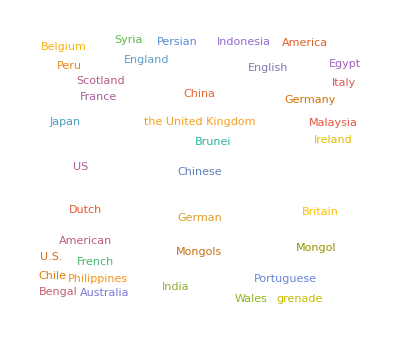

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
TextCases["She sells seashells by the sea shore.","Noun"]
```

{seashells,sea,shore}

```mathematica
Head[WikipediaData["computers"]]
```

String

```mathematica
TextCases[StringTake[WikipediaData["computers"],1000],#]&/@{"Noun","Verb","Adjective"}
```

{{computer,purpose,device,set,operations,sequence,operations,computer,kind,problem,computer,element,processing,unit,form,memory,processing,element,operations,sequencing,control,unit,order,operations,response,information,devices,information,source,result,operations,use,word,computer,book,writer,computer,euer,dayes,number,person},{is,can,be,programmed,carry,can,be,changed,can,solve,consists,processing,carries,can,change,stored,allow,be,retrieved,saved,retrieved,known,was,called,haue,read,breathed,reduceth,referred,c},{general,arithmetic,logical,more,least,central,arithmetic,logic,external,first,truest,best,Arithmetician,thy,short}}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computers"]]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinergeneral
Adjectivepurpose
Noundevice
Noun
Noun Phrase    that
Determiner
Wh-Noun Phrase    can
Verb  be
Verb  programmed
Verb    to
Preposition  carry
Verb  out
Particle
Particle    a
Determinerset
Noun
Noun Phrase  of
Preposition  arithmetic
Nounor
Conjunctionlogical
Adjectiveoperations
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause  automatically
Adverb
Adverb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]
```

<|door→23,voice→22,time→21,way→20,moment→17,thing→17,head→15,table→14,round→13,nothing→12|>

```mathematica
TextStructure[First[TextSentences[WikipediaData["computers"]]],"ConstituentGraphs"]
```

{-Graphics-}

```mathematica
$GeoLocation=GeoPosition[{22.8885312,-109.9128402}] ;
CloudDeploy[GeoListPlot[GeoNearest["Volcano",Here,10]],Permissions->"Public"]
CloudDeploy[FormPage[{"location"->"Location","n"->"Integer"},GeoListPlot[GeoNearest["Volcano",#location,#n]]&]]
```

CloudObject[]

CloudObject[]

```mathematica
(* wikipedia article word cloud *)

CloudDeploy[FormPage[{"wikipedia"->"String"},WordCloud[DeleteStopwords[TextWords[WikipediaData[#wikipedia]]]]&]]
```

CloudObject[]

```mathematica
CloudDeploy[FormPage[{"n"->"Number"},Graphics[Style[RegularPolygon[#n],RandomColor[]]]&]]
```

CloudObject[]

```mathematica
CloudDeploy[FormPage[{"location"->"Location","n"->Integer},GeoListPlot[GeoNearest["Volcano",#location,"n"]]&]]
```

CloudObject[]

```mathematica
f[n_Integer,s_String]:=Nearest[WordList[],s,n]
f[10,"pie"]
f[6,"string"]
```

{pie,die,fie,hie,lie,pee,pi,pic,pied,pier}

{string,spring,staring,sting,strings,stringy}

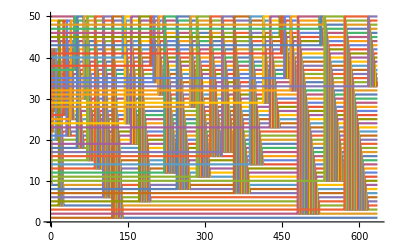

```mathematica
(* Bubble Sort pg 250 *)
{5,4,1,3,2}/.{a___,b_,c_,d___}/;b>c->{a,c,b,d};
NestList[#/.{a___,b_,c_,d___}/;b>c->{a,c,b,d}&,{5,4,1,3,2},10] //Grid;
Transpose[FixedPointList[#/.{a___,b_,c_,d___}/;b>c->{a,c,b,d}&,RandomSample[Range[50]]]]//ListLinePlot
```

```mathematica
FromDigits/@Cases[Table[IntegerDigits[n^2],{n,100}],{___,m_,m_,___}]
```

{100,144,225,400,441,900,1156,1225,1444,1600,2116,2209,2500,3364,3600,3844,4225,4489,4900,5776,6400,6889,7225,7744,8100,8836,10000}

```mathematica
Cases[Characters/@Array[RomanNumeral,100],{___,"L",___,"I",___,"X",___}]
```

{{X,L,I,X},{L,I,X},{L,X,I,X},{L,X,X,I,X},{L,X,X,X,I,X}}

```mathematica
Clear[f]
?f
f[m:{_Integer..}]:=If[m==Reverse[m],"yay!","nope"]
f[{4,5,6,6,5,4}]
f[{4,5,6,5,4}]
f[{4,5,6,5}]
```

Global`f

yay!

yay!

nope

```mathematica
(* Newton's mehtod with rounding *)
FixedPointList[(#+2/#)/2&,1.0]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421}

```mathematica
(* Euclid's GCD *)
Clear[f];
f[{a_Integer,b_Integer}]:=If[b==0,{a,b},f[{b,Mod[a,b]}]]
f[{12345,54321}]
FixedPointList[#/.{a_,b_}/;b≠0->{b,Mod[a,b]}&,{12345,54321}] (* the book's answer : apply rule and the rule -> has condition /; *)
```

{3,0}

{{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}}

```mathematica
FixedPointList[#/.{s[x_][y_][z_]->x[z][y[z]],k[x_][y_]->x}&,s[s][k][s[s[s]][s]][s]]
```

{s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]}

```mathematica
100!
IntegerDigits[100!]/.{x___,0..}->{x}//FromDigits
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864

```mathematica
Length/@NestList[#/.{{1,_,x___}->{x,0,1},{0,_,x___}->{x,1,0,0}}&,{1,0},200]
```

{2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125}

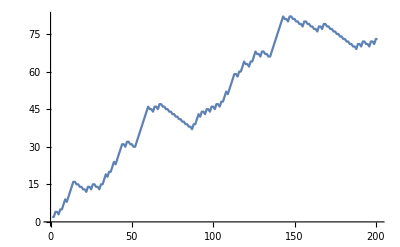

```mathematica
ListLinePlot[Length/@NestList[#/.{{0,_,x___}->{x,2,1},{1,_,x___}->{x,0},{2,_,x___}->{x,0,2,1,2}}&,{0,0},200]]
```

```mathematica
StringReplace["1 2 3 4"," "->"---"]
```

1---2---3---4

```mathematica
Sort@StringCases[WikipediaData["computers"],DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter]
```

{1000,1235,1357,1357,1500,1595,1613,1620,1630,1770,1833,1872,1872,1876,1876,1888,1901,1906,1920,1927,1930,1934,1936,1936,1938,1939,1941,1942,1943,1943,1943,1944,1945,1945,1945,1945,1947,1947,1947,1948,1950,1950,1951,1951,1952,1953,1953,1955,1955,1955,1957,1958,1958,1959,1970,1970,1990,2000,2000,2013,2400,2400,2468,4004,5000}

```mathematica
StringCases[WikipediaData["computers"],Shortest["==="~~x__~~"==="]->x]
```

{ Pre-twentieth century , First computing device , Analog computers , Digital Computers ,= Electromechanical ,= Vacuum tubes and digital electronic circuits , Modern computers ,= The concept of modern computer ,= Stored programs ,= Transistors ,= Integrated circuits , Mobile computers become dominant , Stored program architecture , Machine code , Programming language ,= Low-level languages ,= High-level languages/Third Generation Language , Fourth Generation Languages , Program design , Bugs , Control unit , Central processing unit (CPU) , Arithmetic logic unit (ALU) , Memory , Input/output (I/O) , Multitasking , Multiprocessing , Computer architecture paradigms , Unconventional computing , Artificial intelligence , History of computing hardware , Other hardware topics , Firmware , Based on uses , Based on sizes }

```mathematica
Table[StringTemplate["`1`+`2`=`3`"][i,j,i+j],{i,9},{j,9}]//Grid
```

1+1=2 | 1+2=3 | 1+3=4 | 1+4=5 | 1+5=6 | 1+6=7 | 1+7=8 | 1+8=9 | 1+9=10
2+1=3 | 2+2=4 | 2+3=5 | 2+4=6 | 2+5=7 | 2+6=8 | 2+7=9 | 2+8=10 | 2+9=11
3+1=4 | 3+2=5 | 3+3=6 | 3+4=7 | 3+5=8 | 3+6=9 | 3+7=10 | 3+8=11 | 3+9=12
4+1=5 | 4+2=6 | 4+3=7 | 4+4=8 | 4+5=9 | 4+6=10 | 4+7=11 | 4+8=12 | 4+9=13
5+1=6 | 5+2=7 | 5+3=8 | 5+4=9 | 5+5=10 | 5+6=11 | 5+7=12 | 5+8=13 | 5+9=14
6+1=7 | 6+2=8 | 6+3=9 | 6+4=10 | 6+5=11 | 6+6=12 | 6+7=13 | 6+8=14 | 6+9=15
7+1=8 | 7+2=9 | 7+3=10 | 7+4=11 | 7+5=12 | 7+6=13 | 7+7=14 | 7+8=15 | 7+9=16
8+1=9 | 8+2=10 | 8+3=11 | 8+4=12 | 8+5=13 | 8+6=14 | 8+7=15 | 8+8=16 | 8+9=17
9+1=10 | 9+2=11 | 9+3=12 | 9+4=13 | 9+5=14 | 9+6=15 | 9+7=16 | 9+8=17 | 9+9=18

```mathematica
StringCases[IntegerName[#]&/@Range[50],___~~"i"~~___~~"e"~~___]//Flatten//AbsoluteTiming
Select[Table[IntegerName[n],{n,50}],StringMatchQ[#,___~~"i"~~___~~"e"~~___]&]//AbsoluteTiming
```

{0.006581,{five,nine,thirteen,fifteen,sixteen,eighteen,nineteen,twenty-five,twenty-nine,thirty-one,thirty-three,thirty-five,thirty-seven,thirty-eight,thirty-nine,forty-five,forty-nine}}

{0.007638,{five,nine,thirteen,fifteen,sixteen,eighteen,nineteen,twenty-five,twenty-nine,thirty-one,thirty-three,thirty-five,thirty-seven,thirty-eight,thirty-nine,forty-five,forty-nine}}

```mathematica
StringReplace[First[TextSentences[WikipediaData["computers"]]],x:{WhitespaceCharacter~~_ ~~_~~WhitespaceCharacter}:>ToUpperCase[x]]
```

A computer IS a general purpose device that can BE programmed TO carry out a set OF arithmetic OR logical operations automatically.

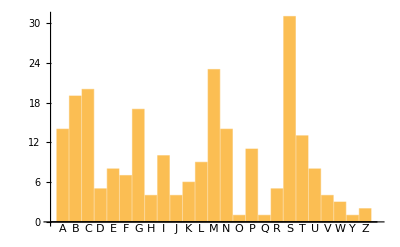

```mathematica
BarChart[KeySort[Counts[StringTake[TextString/@EntityList[EntityClass["Country","Countries"]],1]]],ChartLabels->Automatic]
```

```mathematica
Table[StringJoin[TextString[i],"^",TextString[j],"=",TextString[i^j]],{i,5},{j,5}]//Grid
```

1^1=1 | 1^2=1 | 1^3=1 | 1^4=1 | 1^5=1
2^1=2 | 2^2=4 | 2^3=8 | 2^4=16 | 2^5=32
3^1=3 | 3^2=9 | 3^3=27 | 3^4=81 | 3^5=243
4^1=4 | 4^2=16 | 4^3=64 | 4^4=256 | 4^5=1024
5^1=5 | 5^2=25 | 5^3=125 | 5^4=625 | 5^5=3125